```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/fluc_T/fluctuations_T/highorder_2p1/input_h/finitemub_v4/fluc_Tc230a0p5_h14

### Lattice

```mathematica
HotQCDp=Flatten[Import["../../../../LQCDdata/hotPT4.dat"]];
HotQCDT=Flatten[Import["../../../../LQCDdata/hotT.dat"]];
HotQCDperrdown=Flatten[Import["../../../../LQCDdata/hotdpt4d.dat"]];
HotQCDperrup=Flatten[Import["../../../../LQCDdata/hotdpt4u.dat"]];
Tcl=1;
Hotpdown=Transpose[{HotQCDT/Tcl,HotQCDp+HotQCDperrdown}];
Hotpup=Transpose[{HotQCDT/Tcl,HotQCDp+HotQCDperrup}];
WBp=Flatten[Import["../../../../LQCDdata/wbpt4.dat"]];
WBdp=Flatten[Import["../../../../LQCDdata/wbdpt4.dat"]];
WBT=Flatten[Import["../../../../LQCDdata/wbT.dat"]];
WBdown=Transpose[{WBT/Tcl,WBp-WBdp}];
WBup=Transpose[{WBT/Tcl,WBp+WBdp}];
WBcs=Table[Import["../../../../LQCDdata/WB-EoS.dat"][[i]][[-2]],{i,2,63}];
WBcserr=Table[Import["../../../../LQCDdata/WB-EoS.dat"][[i]][[-1]],{i,2,63}];
WBcsup=Transpose[{WBT/Tcl,WBcs+WBcserr}];
WBcsdown=Transpose[{WBT/Tcl,WBcs-WBcserr}];
WBp2025=Flatten[Import["../../../../LQCDdata/WB2025/PT4WB.dat"]];
WBdp2025=Flatten[Import["../../../../LQCDdata/WB2025/PT4WB_erro.dat"]];
WBT2025=Flatten[Import["../../../../LQCDdata/WB2025/TWB.dat"]];
WBdown2025=Transpose[{WBT2025/Tcl,WBp2025-WBdp2025}];
WBup2025=Transpose[{WBT2025/Tcl,WBp2025+WBdp2025}];
```

### Model

```mathematica
mub={0,25,50,75,100,125,150,175,200,225,250,275,300,325,350,375,400,425,450,475,500,505,510,515,520,525,530,535,540,545,550,555};
T=Table[i,{i,21,300}];
poT4data=Table[(Flatten[Import["./mub"<>ToString[mub[[i]]]<>"/data/chi0.dat"]]-Flatten[Import["./mub"<>ToString[mub[[i]]]<>"/data/chi0.dat"]][[1]])/T^4,{i,1,Length[mub]}];
chi2data=Table[Flatten[Import["./mub"<>ToString[mub[[i]]]<>"/data/chi2.dat"]],{i,1,Length[mub]}];chi3data=Table[Flatten[Import["./mub"<>ToString[mub[[i]]]<>"/data/chi3.dat"]],{i,1,Length[mub]}];chi4data=Table[Flatten[Import["./mub"<>ToString[mub[[i]]]<>"/data/chi4.dat"]],{i,1,Length[mub]}];
c2data=Table[T^2 chi2data[[i]]^-1,{i,1,Length[mub]}];
c3data=Table[-T^5(1/chi2data[[i]])^3(chi3data[[i]]),{i,1,Length[mub]}];
c4data=Table[T^8(3(1/chi2data[[i]])^5(chi3data[[i]])^2-(1/chi2data[[i]])^4 chi4data[[i]]),{i,1,Length[mub]}];
(*Export["./T.dat",T];
Export["./mub.dat",mub];
Export["./c2data.dat",c2data];*)
```

```mathematica
PlotP=Show[ListLinePlot[{Transpose[{T,poT4data[[1]]}],Hotpdown,Hotpup},Filling->{2->{3}},FillingStyle->LightRed,PlotStyle->{Automatic,None,None,Automatic,Automatic,Automatic,Automatic,Automatic,Automatic}(*,PlotLegends->{"PQM Nf=2+1"}*),PlotRange->{{0.,300},{0,4}}],ListLinePlot[{WBdown,WBup},Filling->{1->{2}},PlotStyle->{None}],AxesLabel->{"T","P/T^4"}]
```

ListLinePlot::lpn: {{{21.,0.},{22.,0.00188162},{23.,0.00369443},{24.,0.00544755},{25.,0.00713844},{26.,0.00875798},{27.,0.0102939},{28.,0.0117333},{29.,0.0130649},{30.,0.01428},«270»},{},{}} 不是由数字或者数对组成的列表.

Show::gcomb: 无法合并 Show[«1»] 中的图形对象.

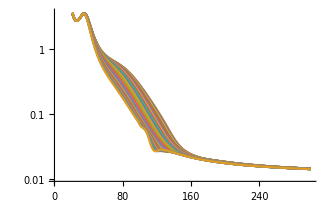

```mathematica
ListLinePlot[Table[Transpose[{T,c2data[[i]]}],{i,1,Length[mub]}],ScalingFunctions->"Log"]
```

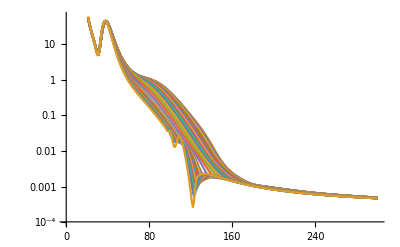

```mathematica
ListLinePlot[Table[Transpose[{T,-c3data[[i]]}],{i,1,Length[mub]}],ScalingFunctions->"Log"]
```

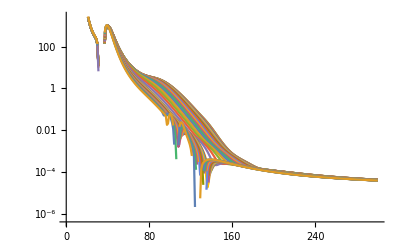

```mathematica
ListLinePlot[Table[Transpose[{T,c4data[[i]]}],{i,1,Length[mub]}],ScalingFunctions->"Log"]
```

```mathematica
c2heatdata=Flatten[Table[{x=mub[[j]],y=T[[i]],c2data[[j]][[i]]},{i,1,Length[T]},{j,1,Length[mub]}],1];
c3heatdata=Flatten[Table[{x=mub[[j]],y=T[[i]],c3data[[j]][[i]]},{i,1,Length[T]},{j,1,Length[mub]}],1];
c4heatdata=Flatten[Table[{x=mub[[j]],y=T[[i]],c4data[[j]][[i]]},{i,1,Length[T]},{j,1,Length[mub]}],1];
c2int=Interpolation[c2heatdata];
c3int=Interpolation[c3heatdata];
c4int=Interpolation[c4heatdata];
c2intdata=Table[c2int[x1,y1],{x1,0,555,1},{y1,21,300,1}];
c3intdata=Table[c3int[x1,y1],{x1,0,555,1},{y1,21,300,1}];
c4intdata=Table[c4int[x1,y1],{x1,0,555,1},{y1,21,300,1}];
mub=Table[i,{i,1,555,1}];
T=Table[i,{i,21,300,1}];
Export["c2data.dat",c2intdata];
Export["c3data.dat",c3intdata];
Export["c4data.dat",c4intdata];
Export["mub.dat",mub];
Export["T.dat",T];
(*Show[ListLinePlot[Table[Transpose[{T,c2data[[i]]}],{i,1,1}],ScalingFunctions->"Log",PlotStyle->Black],Plot[c2int[0,y1],{y1,21,300},ScalingFunctions->"Log",PlotStyle->{Red,Dashed}]]*)
```

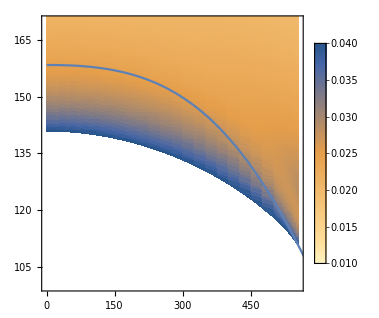

```mathematica
zMin=0.01;
zMax=0.04;
Show[ListDensityPlot[c2heatdata,ColorFunctionScaling->False,ColorFunction->(ColorData["M10DefaultDensityGradient"][1-Rescale[#,{zMin,zMax}]]&),PlotRange->{Automatic,{100,170},{zMin,zMax}},PlotLegends->BarLegend[{Automatic,{zMin,zMax}}]],Plot[Tfo[x1],{x1,0,600}]]
```

### Freeze-out line

```mathematica
mubfo[sqrts_]:=1307.5/(1+0.288 sqrts);
sqrts[muB_]:=-(1.7361111111111112 (-2615.+2. muB))/muB;
Tfo[muB_]:=158.4/(1+Exp[2.60-Log[(1307.5/muB-1)/0.288]/0.45]);
(*Tfo[muB_]:=158.4/(1+Exp[2.60-Log[(1307.5/(muB/1.25)-1)/0.288]/0.45])-10;*)
data=Table[Transpose[{T,c2data[[i]]}],{i,1,Length[mub]}];datac3=Table[Transpose[{T,c3data[[i]]}],{i,1,Length[mub]}];datac4=Table[Transpose[{T,c4data[[i]]}],{i,1,Length[mub]}];
intfun=Table[Interpolation[data[[i]]],{i,1,Length[mub]}];intfunc3=Table[Interpolation[datac3[[i]]],{i,1,Length[mub]}];intfunc4=Table[Interpolation[datac4[[i]]],{i,1,Length[mub]}];
c2fo=Table[{sqrts[mub[[i]]],intfun[[i]][Tfo[mub[[i]]]]},{i,2,Length[mub]}];c3fo=Table[{sqrts[mub[[i]]],intfunc3[[i]][Tfo[mub[[i]]]]},{i,2,Length[mub]}];c4fo=Table[{sqrts[mub[[i]]],intfunc4[[i]][Tfo[mub[[i]]]]},{i,2,Length[mub]}];
STARFitI=Transpose[{Flatten[Import["./freezeout/mub.dat"]],Flatten[Import["./freezeout/STARFitI.dat"]]}];
STARFitII=Transpose[{Flatten[Import["./freezeout/mub.dat"]],Flatten[Import["./freezeout/STARFitII.dat"]]}];
TI=Table[Interpolation[STARFitI][mub[[i]]],{i,2,Length[mub]}];
TII=Table[Interpolation[STARFitII][mub[[i]]],{i,2,Length[mub]}];
c2foI=Table[{sqrts[mub[[i]]],(intfun[[i]][TI[[i-1]]])/((*TI[[i-1]]*)1)},{i,2,Length[mub]}];
c2foII=Table[{sqrts[mub[[i]]],(intfun[[i]][TII[[i-1]]])/((*TII[[i-1]]*)1)},{i,2,Length[mub]}];
c3foI=Table[{sqrts[mub[[i]]],(intfunc3[[i]][TI[[i-1]]])/((*TI[[i-1]]*)1)},{i,2,Length[mub]}];
c3foII=Table[{sqrts[mub[[i]]],(intfunc3[[i]][TII[[i-1]]])/((*TII[[i-1]]*)1)},{i,2,Length[mub]}];
c4foI=Table[{sqrts[mub[[i]]],(intfunc4[[i]][TI[[i-1]]])/((*TI[[i-1]]*)1)},{i,2,Length[mub]}];
c4foII=Table[{sqrts[mub[[i]]],(intfunc4[[i]][TII[[i-1]]])/((*TII[[i-1]]*)1)},{i,2,Length[mub]}];
```

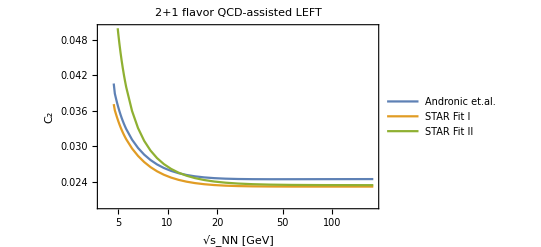

```mathematica
ListLinePlot[{c2fo,c2foI,c2foII},PlotRange->{All,{0.02,0.05}},ScalingFunctions->{"Log",Automatic},PlotLegends->{"Andronic et.al.","STAR Fit I","STAR Fit II"},Frame->True,FrameLabel->{Style["√s_NN [GeV]",Black,15,FontFamily->"Times New Roman"],Style["C_2",Black,15,FontFamily->"Times New Roman"]},PlotLabel->Style["2+1 flavor QCD-assisted LEFT",Black,15,FontFamily->"Times New Roman"]]
```

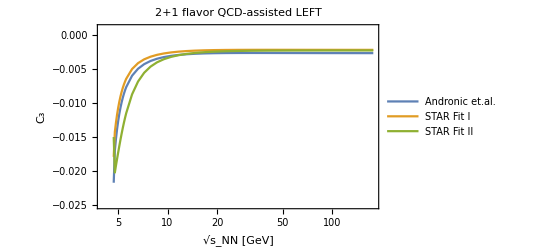

```mathematica
ListLinePlot[{c3fo,c3foI,c3foII},PlotRange->{All,{-0.025,0.001}},ScalingFunctions->{"Log",Automatic},PlotLegends->{"Andronic et.al.","STAR Fit I","STAR Fit II"},Frame->True,FrameLabel->{Style["√s_NN [GeV]",Black,15,FontFamily->"Times New Roman"],Style["C_3",Black,15,FontFamily->"Times New Roman"]},PlotLabel->Style["2+1 flavor QCD-assisted LEFT",Black,15,FontFamily->"Times New Roman"]]
```

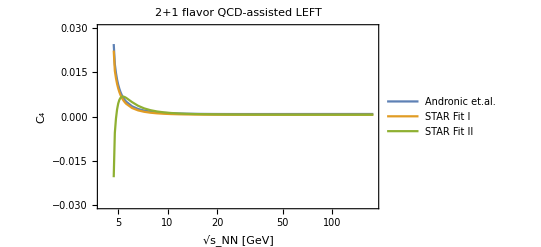

```mathematica
ListLinePlot[{c4fo,c4foI,c4foII},PlotRange->{All,{-0.03,0.03}},ScalingFunctions->{"Log",Automatic},PlotLegends->{"Andronic et.al.","STAR Fit I","STAR Fit II"},Frame->True,FrameLabel->{Style["√s_NN [GeV]",Black,15,FontFamily->"Times New Roman"],Style["C_4",Black,15,FontFamily->"Times New Roman"]},PlotLabel->Style["2+1 flavor QCD-assisted LEFT",Black,15,FontFamily->"Times New Roman"]]
```

```mathematica
Export["./Andro_c2.dat",c2fo];
Export["./STARFitI_c2.dat",c2foI];
Export["./STARFitII_c2.dat",c2foII];
Export["./Andro_c3.dat",c3fo];
Export["./STARFitI_c3.dat",c3foI];
Export["./STARFitII_c3.dat",c3foII];
Export["./Andro_c4.dat",c4fo];
Export["./STARFitI_c4.dat",c4foI];
Export["./STARFitII_c4.dat",c4foII];
```